```mathematica
(*Directory[]*)
```

```mathematica
SetDirectory["/Users/rht/Dropbox/projects/physicsproject/comptonscattering/0STUFF/FeynArts-3.5"]
<<FeynArts`
```

"

```mathematica
t22 = CreateTopologies[0,2->2];
aa = InsertFields[t22,{F[1,{1}],V[1]} -> {F[1,{1}],V[1]},InsertionLevel->{Classes}, Model-> QED]; (*use F[2,{1}] for SM model*)
(*aa = InsertFields[t22,F[2]-> F[2] ];*)
aamp = CreateFeynAmp[aa]
Paint[aa]
(*amp>>PhotonSelfEnergy.amp*)
```

```mathematica
tcube = CreateTopologies[3,1->1];
aa = InsertFields[tcube,F[1,{1}] -> F[1,{1}],InsertionLevel->{Classes}, Model-> QED]; (*use F[2,{1}] for SM model*)
(*aa = InsertFields[tcube,F[2]-> F[2] ];*)
(*aamp = CreateFeynAmp[aa]*)
Paint[aa]
```

loading classes model file /Users/rht/Dropbox/projects/physicsproject/comptonscattering/0STUFF/feynarts-3.5/Models/QED.mod

> 7 particles (incl. antiparticles) in 2 classes

> $CounterTerms are ON

> 1 vertices

> 3 counter terms of order 1

classes model {QED} initialized

inserting at level(s) {Classes}

Graph::optrs: Option specification Field[9] → 0 in Graph[Field[1] → F[1, {1}], Field[2] → -F[1, {1}], Field[3] → 0, Field[4] → 0, Field[5] → 0, Field[6] → 0, Field[7] → 0, Field[8] → 0, Field[9] → 0] is not a rule for a symbol or string.

Graph::optrs: Option specification Field[9] → 0 in Graph[Field[1] → F[1], Field[2] → -F[1], Field[3] → 0, Field[4] → 0, Field[5] → 0, Field[6] → 0, Field[7] → 0, Field[8] → 0, Field[9] → 0] is not a rule for a symbol or string.

Graph::optrs: Option specification Field[9] → 0 in Graph[Field[1] → F, Field[2] → F, Field[3] → 0, Field[4] → 0, Field[5] → 0, Field[6] → 0, Field[7] → 0, Field[8] → 0, Field[9] → 0] is not a rule for a symbol or string.

General::stop: Further output of Graph :: optrs will be suppressed during this calculation.

> Top. 1: 0 Classes insertions

> Top. 2: 4 Classes insertions

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

> Top. 5: 0 Classes insertions

> Top. 6: 0 Classes insertions

> Top. 7: 0 Classes insertions

> Top. 8: 0 Classes insertions

> Top. 9: 0 Classes insertions

> Top. 10: 0 Classes insertions

> Top. 11: 0 Classes insertions

> Top. 12: 0 Classes insertions

> Top. 13: 0 Classes insertions

> Top. 14: 0 Classes insertions

> Top. 15: 0 Classes insertions

> Top. 16: 0 Classes insertions

> Top. 17: 0 Classes insertions

> Top. 18: 0 Classes insertions

> Top. 19: 0 Classes insertions

> Top. 20: 0 Classes insertions

> Top. 21: 0 Classes insertions

> Top. 22: 0 Classes insertions

> Top. 23: 0 Classes insertions

> Top. 24: 0 Classes insertions

> Top. 25: 0 Classes insertions

> Top. 26: 0 Classes insertions

> Top. 27: 0 Classes insertions

> Top. 28: 0 Classes insertions

> Top. 29: 0 Classes insertions

> Top. 30: 0 Classes insertions

> Top. 31: 1 Classes insertion

> Top. 32: 3 Classes insertions

> Top. 33: 1 Classes insertion

> Top. 34: 2 Classes insertions

> Top. 35: 1 Classes insertion

> Top. 36: 2 Classes insertions

> Top. 37: 2 Classes insertions

> Top. 38: 4 Classes insertions

> Top. 39: 0 Classes insertions

> Top. 40: 0 Classes insertions

> Top. 41: 0 Classes insertions

> Top. 42: 0 Classes insertions

> Top. 43: 0 Classes insertions

> Top. 44: 0 Classes insertions

> Top. 45: 0 Classes insertions

> Top. 46: 0 Classes insertions

> Top. 47: 0 Classes insertions

> Top. 48: 0 Classes insertions

> Top. 49: 0 Classes insertions

> Top. 50: 0 Classes insertions

> Top. 51: 0 Classes insertions

> Top. 52: 0 Classes insertions

> Top. 53: 0 Classes insertions

> Top. 54: 0 Classes insertions

> Top. 55: 0 Classes insertions

> Top. 56: 0 Classes insertions

> Top. 57: 0 Classes insertions

> Top. 58: 0 Classes insertions

> Top. 59: 0 Classes insertions

> Top. 60: 0 Classes insertions

> Top. 61: 0 Classes insertions

> Top. 62: 0 Classes insertions

> Top. 63: 0 Classes insertions

> Top. 64: 0 Classes insertions

> Top. 65: 0 Classes insertions

> Top. 66: 0 Classes insertions

> Top. 67: 0 Classes insertions

> Top. 68: 0 Classes insertions

> Top. 69: 0 Classes insertions

> Top. 70: 0 Classes insertions

> Top. 71: 0 Classes insertions

> Top. 72: 0 Classes insertions

> Top. 73: 0 Classes insertions

> Top. 74: 0 Classes insertions

> Top. 75: 0 Classes insertions

> Top. 76: 0 Classes insertions

> Top. 77: 0 Classes insertions

> Top. 78: 0 Classes insertions

> Top. 79: 0 Classes insertions

> Top. 80: 0 Classes insertions

> Top. 81: 0 Classes insertions

> Top. 82: 0 Classes insertions

> Top. 83: 0 Classes insertions

> Top. 84: 0 Classes insertions

> Top. 85: 0 Classes insertions

> Top. 86: 0 Classes insertions

> Top. 87: 0 Classes insertions

> Top. 88: 0 Classes insertions

> Top. 89: 0 Classes insertions

> Top. 90: 0 Classes insertions

> Top. 91: 0 Classes insertions

> Top. 92: 0 Classes insertions

> Top. 93: 0 Classes insertions

> Top. 94: 0 Classes insertions

> Top. 95: 0 Classes insertions

> Top. 96: 0 Classes insertions

> Top. 97: 0 Classes insertions

> Top. 98: 0 Classes insertions

> Top. 99: 0 Classes insertions

> Top. 100: 0 Classes insertions

> Top. 101: 0 Classes insertions

> Top. 102: 0 Classes insertions

> Top. 103: 0 Classes insertions

> Top. 104: 0 Classes insertions

> Top. 105: 0 Classes insertions

> Top. 106: 0 Classes insertions

> Top. 107: 0 Classes insertions

> Top. 108: 0 Classes insertions

> Top. 109: 0 Classes insertions

> Top. 110: 0 Classes insertions

> Top. 111: 0 Classes insertions

> Top. 112: 0 Classes insertions

> Top. 113: 0 Classes insertions

> Top. 114: 0 Classes insertions

> Top. 115: 0 Classes insertions

> Top. 116: 0 Classes insertions

> Top. 117: 0 Classes insertions

> Top. 118: 0 Classes insertions

> Top. 119: 0 Classes insertions

> Top. 120: 0 Classes insertions

> Top. 121: 0 Classes insertions

> Top. 122: 0 Classes insertions

> Top. 123: 0 Classes insertions

> Top. 124: 0 Classes insertions

> Top. 125: 0 Classes insertions

> Top. 126: 0 Classes insertions

> Top. 127: 0 Classes insertions

> Top. 128: 0 Classes insertions

> Top. 129: 0 Classes insertions

> Top. 130: 0 Classes insertions

> Top. 131: 0 Classes insertions

> Top. 132: 0 Classes insertions

> Top. 133: 0 Classes insertions

> Top. 134: 0 Classes insertions

> Top. 135: 0 Classes insertions

> Top. 136: 0 Classes insertions

> Top. 137: 0 Classes insertions

> Top. 138: 1 Classes insertion

> Top. 139: 2 Classes insertions

> Top. 140: 2 Classes insertions

> Top. 141: 1 Classes insertion

> Top. 142: 1 Classes insertion

> Top. 143: 1 Classes insertion

> Top. 144: 1 Classes insertion

> Top. 145: 1 Classes insertion

> Top. 146: 1 Classes insertion

> Top. 147: 1 Classes insertion

> Top. 148: 1 Classes insertion

> Top. 149: 2 Classes insertions

> Top. 150: 1 Classes insertion

> Top. 151: 2 Classes insertions

> Top. 152: 1 Classes insertion

> Top. 153: 1 Classes insertion

> Top. 154: 1 Classes insertion

> Top. 155: 1 Classes insertion

> Top. 156: 1 Classes insertion

> Top. 157: 1 Classes insertion

> Top. 158: 2 Classes insertions

> Top. 159: 1 Classes insertion

> Top. 160: 2 Classes insertions

> Top. 161: 1 Classes insertion

> Top. 162: 1 Classes insertion

> Top. 163: 2 Classes insertions

> Top. 164: 0 Classes insertions

> Top. 165: 0 Classes insertions

> Top. 166: 0 Classes insertions

> Top. 167: 0 Classes insertions

> Top. 168: 0 Classes insertions

> Top. 169: 0 Classes insertions

> Top. 170: 0 Classes insertions

> Top. 171: 0 Classes insertions

> Top. 172: 0 Classes insertions

> Top. 173: 0 Classes insertions

> Top. 174: 0 Classes insertions

> Top. 175: 0 Classes insertions

> Top. 176: 0 Classes insertions

> Top. 177: 0 Classes insertions

> Top. 178: 0 Classes insertions

> Top. 179: 0 Classes insertions

> Top. 180: 0 Classes insertions

> Top. 181: 0 Classes insertions

> Top. 182: 0 Classes insertions

> Top. 183: 0 Classes insertions

> Top. 184: 0 Classes insertions

> Top. 185: 0 Classes insertions

> Top. 186: 0 Classes insertions

> Top. 187: 0 Classes insertions

> Top. 188: 0 Classes insertions

> Top. 189: 0 Classes insertions

> Top. 190: 0 Classes insertions

> Top. 191: 0 Classes insertions

> Top. 192: 0 Classes insertions

> Top. 193: 0 Classes insertions

> Top. 194: 0 Classes insertions

> Top. 195: 0 Classes insertions

> Top. 196: 0 Classes insertions

> Top. 197: 0 Classes insertions

> Top. 198: 0 Classes insertions

> Top. 199: 0 Classes insertions

> Top. 200: 0 Classes insertions

> Top. 201: 0 Classes insertions

> Top. 202: 0 Classes insertions

> Top. 203: 0 Classes insertions

> Top. 204: 0 Classes insertions

> Top. 205: 0 Classes insertions

> Top. 206: 0 Classes insertions

> Top. 207: 0 Classes insertions

> Top. 208: 0 Classes insertions

> Top. 209: 0 Classes insertions

> Top. 210: 0 Classes insertions

> Top. 211: 0 Classes insertions

> Top. 212: 0 Classes insertions

> Top. 213: 0 Classes insertions

> Top. 214: 0 Classes insertions

> Top. 215: 0 Classes insertions

> Top. 216: 0 Classes insertions

> Top. 217: 0 Classes insertions

> Top. 218: 0 Classes insertions

> Top. 219: 0 Classes insertions

> Top. 220: 0 Classes insertions

> Top. 221: 0 Classes insertions

> Top. 222: 0 Classes insertions

> Top. 223: 0 Classes insertions

> Top. 224: 0 Classes insertions

> Top. 225: 0 Classes insertions

> Top. 226: 0 Classes insertions

> Top. 227: 0 Classes insertions

> Top. 228: 0 Classes insertions

> Top. 229: 0 Classes insertions

> Top. 230: 0 Classes insertions

> Top. 231: 0 Classes insertions

> Top. 232: 0 Classes insertions

> Top. 233: 0 Classes insertions

> Top. 234: 0 Classes insertions

> Top. 235: 0 Classes insertions

> Top. 236: 0 Classes insertions

> Top. 237: 0 Classes insertions

> Top. 238: 0 Classes insertions

> Top. 239: 0 Classes insertions

> Top. 240: 0 Classes insertions

> Top. 241: 0 Classes insertions

> Top. 242: 0 Classes insertions

> Top. 243: 0 Classes insertions

> Top. 244: 0 Classes insertions

> Top. 245: 0 Classes insertions

> Top. 246: 0 Classes insertions

> Top. 247: 0 Classes insertions

> Top. 248: 0 Classes insertions

> Top. 249: 0 Classes insertions

> Top. 250: 0 Classes insertions

> Top. 251: 0 Classes insertions

> Top. 252: 0 Classes insertions

> Top. 253: 0 Classes insertions

> Top. 254: 0 Classes insertions

> Top. 255: 0 Classes insertions

> Top. 256: 0 Classes insertions

> Top. 257: 0 Classes insertions

> Top. 258: 0 Classes insertions

> Top. 259: 0 Classes insertions

> Top. 260: 0 Classes insertions

> Top. 261: 0 Classes insertions

> Top. 262: 0 Classes insertions

> Top. 263: 0 Classes insertions

> Top. 264: 0 Classes insertions

> Top. 265: 0 Classes insertions

> Top. 266: 0 Classes insertions

> Top. 267: 0 Classes insertions

> Top. 268: 0 Classes insertions

> Top. 269: 0 Classes insertions

> Top. 270: 0 Classes insertions

> Top. 271: 0 Classes insertions

> Top. 272: 0 Classes insertions

> Top. 273: 0 Classes insertions

> Top. 274: 0 Classes insertions

> Top. 275: 0 Classes insertions

> Top. 276: 0 Classes insertions

> Top. 277: 0 Classes insertions

> Top. 278: 0 Classes insertions

> Top. 279: 0 Classes insertions

> Top. 280: 0 Classes insertions

> Top. 281: 0 Classes insertions

> Top. 282: 0 Classes insertions

> Top. 283: 1 Classes insertion

> Top. 284: 1 Classes insertion

> Top. 285: 0 Classes insertions

> Top. 286: 0 Classes insertions

> Top. 287: 1 Classes insertion

> Top. 288: 1 Classes insertion

> Top. 289: 0 Classes insertions

> Top. 290: 1 Classes insertion

> Top. 291: 1 Classes insertion

> Top. 292: 1 Classes insertion

> Top. 293: 1 Classes insertion

> Top. 294: 1 Classes insertion

> Top. 295: 1 Classes insertion

> Top. 296: 1 Classes insertion

> Top. 297: 1 Classes insertion

> Top. 298: 1 Classes insertion

> Top. 299: 0 Classes insertions

> Top. 300: 1 Classes insertion

> Top. 301: 1 Classes insertion

> Top. 302: 1 Classes insertion

> Top. 303: 1 Classes insertion

> Top. 304: 1 Classes insertion

> Top. 305: 1 Classes insertion

> Top. 306: 1 Classes insertion

> Top. 307: 1 Classes insertion

> Top. 308: 0 Classes insertions

> Top. 309: 0 Classes insertions

> Top. 310: 0 Classes insertions

> Top. 311: 0 Classes insertions

> Top. 312: 0 Classes insertions

> Top. 313: 0 Classes insertions

> Top. 314: 0 Classes insertions

> Top. 315: 0 Classes insertions

> Top. 316: 0 Classes insertions

> Top. 317: 0 Classes insertions

> Top. 318: 0 Classes insertions

> Top. 319: 0 Classes insertions

> Top. 320: 0 Classes insertions

> Top. 321: 0 Classes insertions

> Top. 322: 0 Classes insertions

> Top. 323: 0 Classes insertions

> Top. 324: 0 Classes insertions

> Top. 325: 0 Classes insertions

> Top. 326: 0 Classes insertions

> Top. 327: 0 Classes insertions

> Top. 328: 0 Classes insertions

> Top. 329: 0 Classes insertions

> Top. 330: 0 Classes insertions

> Top. 331: 0 Classes insertions

> Top. 332: 0 Classes insertions

> Top. 333: 0 Classes insertions

> Top. 334: 0 Classes insertions

> Top. 335: 0 Classes insertions

> Top. 336: 0 Classes insertions

> Top. 337: 0 Classes insertions

> Top. 338: 0 Classes insertions

> Top. 339: 0 Classes insertions

> Top. 340: 0 Classes insertions

> Top. 341: 0 Classes insertions

> Top. 342: 0 Classes insertions

> Top. 343: 0 Classes insertions

> Top. 344: 0 Classes insertions

> Top. 345: 0 Classes insertions

> Top. 346: 0 Classes insertions

> Top. 347: 0 Classes insertions

> Top. 348: 0 Classes insertions

> Top. 349: 0 Classes insertions

> Top. 350: 0 Classes insertions

> Top. 351: 0 Classes insertions

in total: 74 Classes insertions

> Top. 1: 4 diagrams

> Top. 2: 1 diagram

> Top. 3: 3 diagrams

> Top. 4: 1 diagram

> Top. 5: 2 diagrams

> Top. 6: 1 diagram

> Top. 7: 2 diagrams

> Top. 8: 2 diagrams

> Top. 9: 4 diagrams

shaping topology {ac,bc,cdef1d1e212d2eff}

autoshaping

> Top. 1: 1 diagram

> Top. 2: 1 diagram

> Top. 3: 1 diagram

> Top. 4: 1 diagram

> Top. 5: 1 diagram

> Top. 6: 1 diagram

> Top. 7: 1 diagram

> Top. 8: 1 diagram

> Top. 9: 1 diagram

> Top. 10: 1 diagram

> Top. 11: 1 diagram

> Top. 12: 1 diagram

> Top. 13: 1 diagram

> Top. 14: 1 diagram

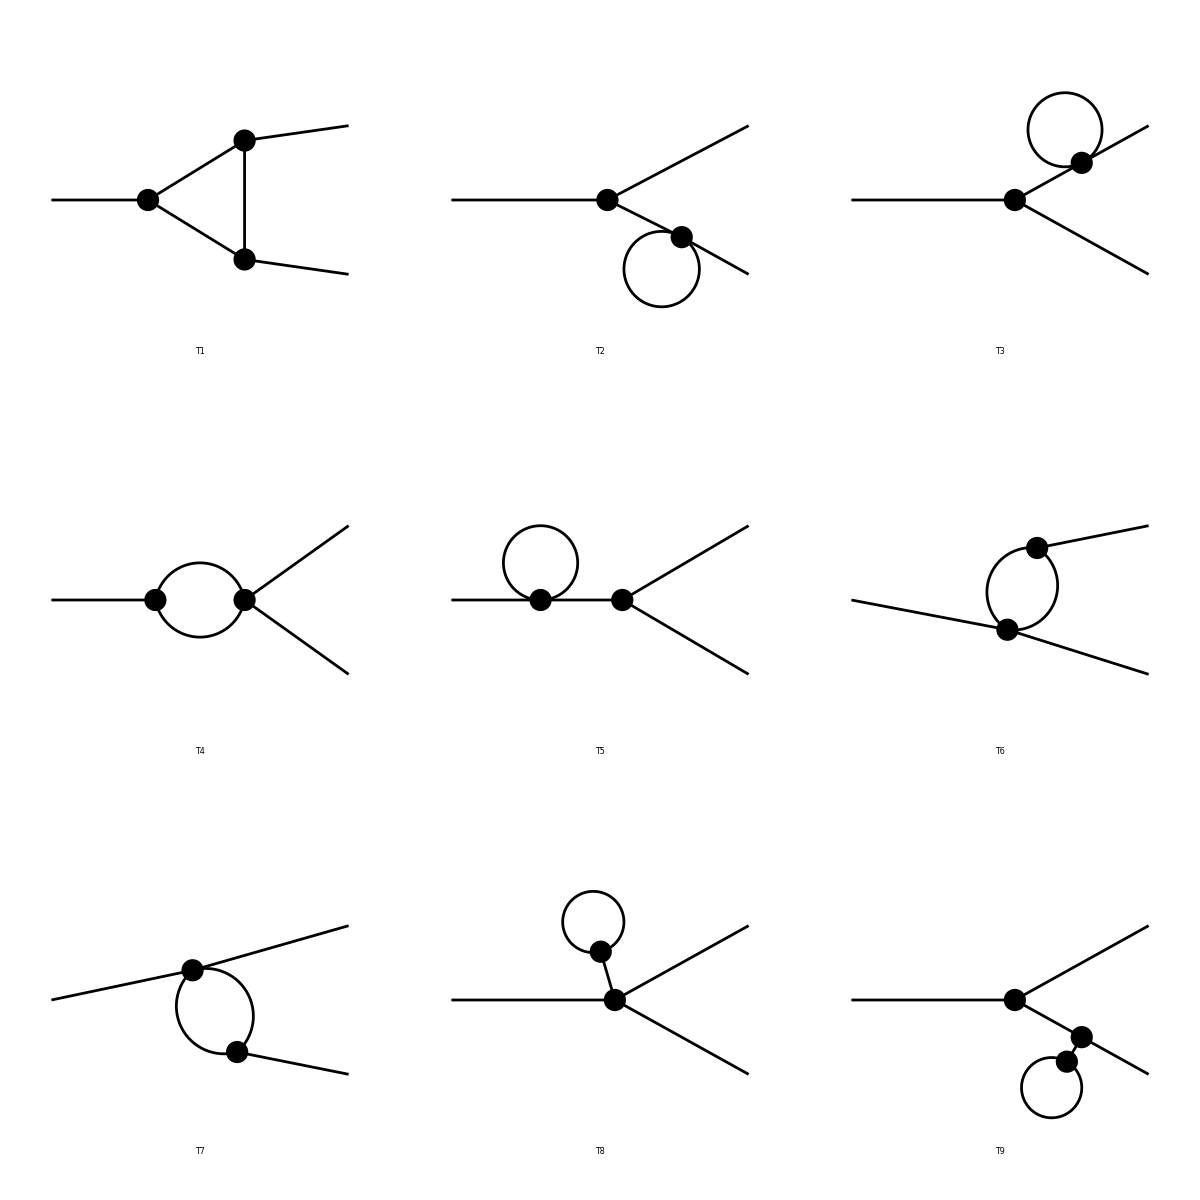

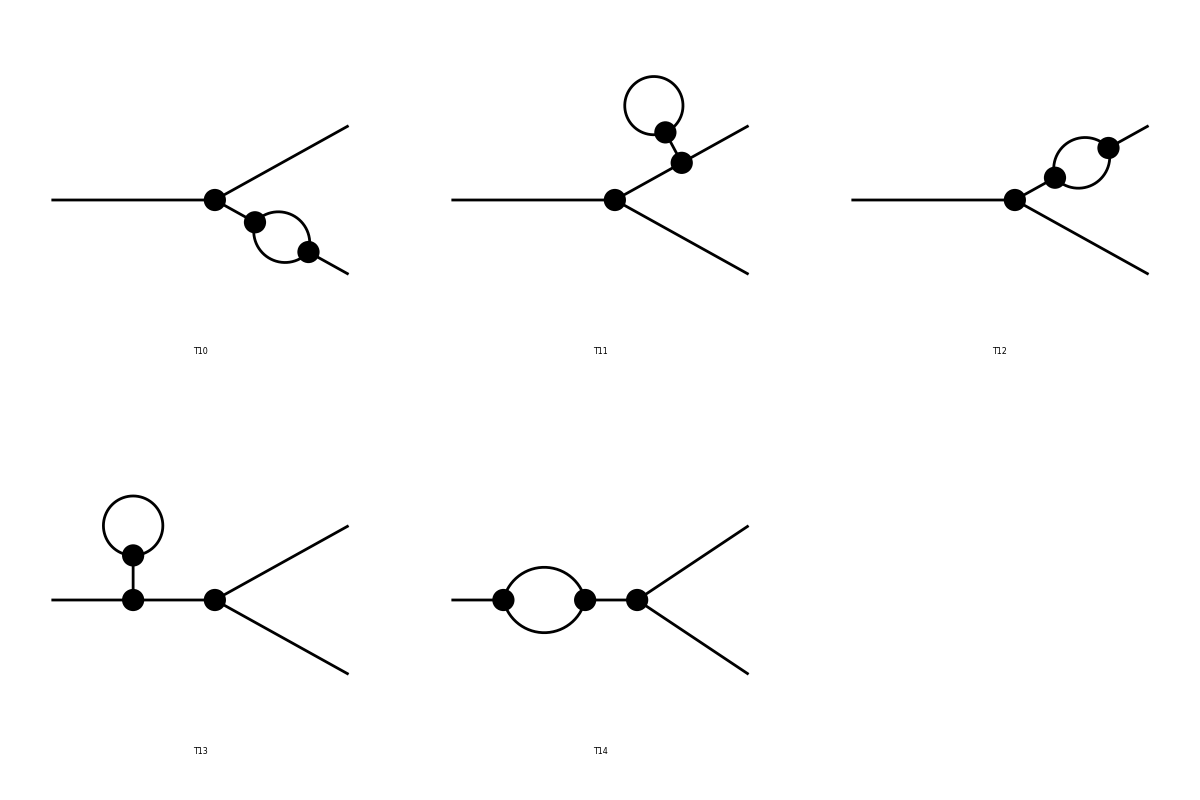

FeynArtsGraphics[1→2][([T1] | [T2] | [T3]
[T4] | [T5] | [T6]
[T7] | [T8] | [T9]),([T10] | [T11] | [T12]
[T13] | [T14] | Null
Null | Null | Null)]

```mathematica
blah = CreateTopologies[1, 1->2];
Paint[blah]
```

```mathematica
(*examine feynarts functions*)
?FeynArts`*
```

```mathematica
tops = CreateTopologies[0,4,ExcludeTopologies->{}];
ins = InsertFields[tops,{F[3,{1}],-F[3,{1}]}->{F[2,{1}],-F[2,{1}]},Model->SMQCD,InsertionLevel->{Classes},ExcludeParticles->{{S[1],S[2],S[3]}}];
Paint[ins,ColumnsXRows->{2,1},PaintLevel->{Classes}];
famp=CreateFeynamp[ins]
famp // Length
strm = OpenWrite["testtestan.amp"]
Write[strm,famp2]
Close[strm]
```